```mathematica
f[x_]=4x^3-9x+6
```

6-9 x+4 x^3

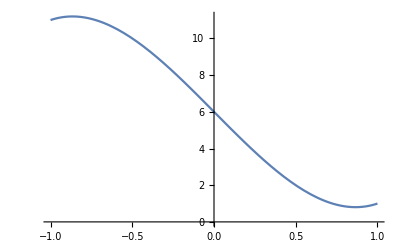

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
{{x->Root"-1.76"Root[6-9 #1+4 #1^3&,1]-1.7611666966796562},{x->Root"0.881"-"0.276" ⅈRoot[6-9 #1+4 #1^3&,2]0.8805833483398281},{x->Root"0.881"+"0.276" ⅈRoot[6-9 #1+4 #1^3&,3]0.8805833483398281}}
Solve[f[x]==0,x]
```

{{x→Root-1.76Root[6-9 #1+4 #1^3&,1]-1.7611666966796562},{x→Root0.881-0.276 ⅈRoot[6-9 #1+4 #1^3&,2]0.8805833483398281},{x→Root0.881+0.276 ⅈRoot[6-9 #1+4 #1^3&,3]0.8805833483398281}}

{{x→Root-1.76Root[6-9 #1+4 #1^3&,1]-1.7611666966796562},{x→Root0.881-0.276 ⅈRoot[6-9 #1+4 #1^3&,2]0.8805833483398281},{x→Root0.881+0.276 ⅈRoot[6-9 #1+4 #1^3&,3]0.8805833483398281}}

```mathematica
x/.{{x->-1.7611666966796562},{x->0.8805833483398281-0.27619033314029895 ⅈ},{x->0.8805833483398281+0.27619033314029895 ⅈ}}
```

```mathematica
FindRoot[f[x],{x,0.8}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→0.866026}

```mathematica
f[-1.7611666966796562]
```

```mathematica
f[-1.7611666966796562]
```

```mathematica
Solve[f'[x]==0,x]
```

{{x→-(√3)/2},{x→(√3)/2}}

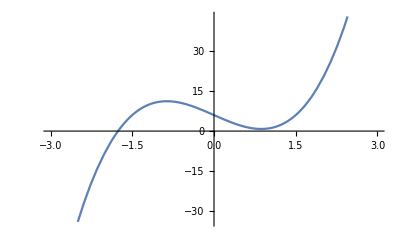

```mathematica
Plot[f[x],{x,-3,3}]
```

```mathematica
Solve[f'[x]==0,x]
```

{{x→-(√3)/2},{x→(√3)/2}}

```mathematica
f[(√3)/2]
```

6-3 √3

```mathematica
f'[-1]
```

3

```mathematica
g[x_]=√(1-√(3-x^2))
```

√(1-√(3-x^2))

```mathematica
Solve[√(3-x^2)==0,x]
```

```mathematica
{{x->-√3},{x->√3}}
```

{{x→-√3},{x→√3}}

```mathematica
Solve[√(1-√(3-x^2))==0]
```

```mathematica
{{x->-√2},{x->√2}}
```

{{x→-√2},{x→√2}}

```mathematica
Simplify[g[x]-g[-x],x]
```

0

```mathematica
y[x_]=2x-7
```

Set::write: Tag Plus in (-7+2 x)[x_] is Protected.

-7+2 x

```mathematica
Plot[y[x],{x,-20,20}]
```

-Graphics-

```mathematica
h[x_]=x*Cos[x]
```

x Cos[x]

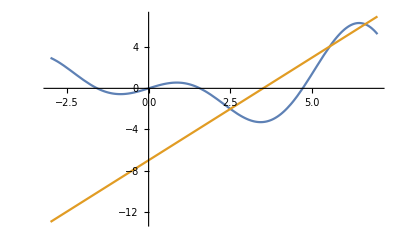

```mathematica
Plot[{h[x],2x-7},{x,-3,7}]
```

```mathematica
NSolve[{h[x]==2x-7},x,Reals]
```

{{x→2.49933},{x→5.54032},{x→6.62247}}

```mathematica
h[6.622470813924581]
```

6.24494

```mathematica
p[x_]=60x^3-14x+1
```

1-14 x+60 x^3

```mathematica
q[x_]=18x^3-25x^2+9
```

9-25 x^2+18 x^3

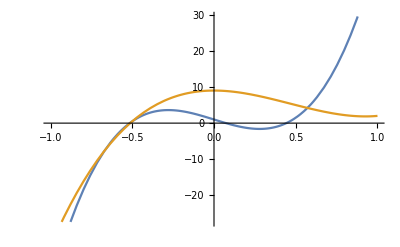

```mathematica
Plot[{p[x],q[x]},{x,-1,1}]
```

```mathematica
Solve[{p[x]==q[x]},x]
```

{{x→-2/3},{x→-1/2},{x→4/7}}

```mathematica
Abs[Integrate[p[x],{x,-2/3,-1/2}]-Integrate[q[x],{x,-2/3,-1/2}]]+Abs[Integrate[p[x],{x,-1/2,4/7}]-Integrate[q[x],{x,-1/2,4/7}]]
```

2704823/444528

```mathematica
N[%]
```

6.08471

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
i[x_]=Sin[x]/(1+x)
```

Sin[x]/(1+x)

```mathematica
Abs[NIntegrate[i[x],{x,0,Pi}]]
```

0.843811

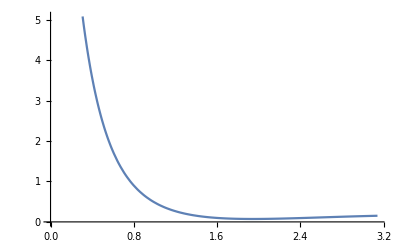

```mathematica
Plot[Abs[i''''[x]],{x,0,Pi}]
```

```mathematica
Simpson[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+4*Sum[f[a+(2*k+1)*h],{k,0,n/2-1}]+2*Sum[f[a+2*k*h],{k,1,n/2-1}]+f[b])*h/3,20] ]
```

```mathematica
Simpson[i,{Pi,0,50}]
```

-0.84381039750737486752

```mathematica
NSolve[(Pi-0)^5/(180*(50^4))*5]
```

{}

```mathematica
f[x]
```

6-9 x+4 x^3

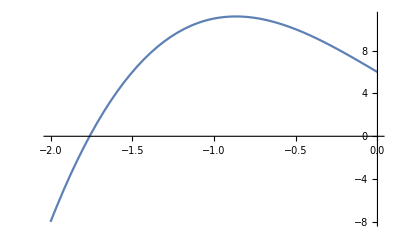

```mathematica
Plot[f[x],{x,-2,0}]
```

```mathematica
Solve[f'[-1]]
```

Solve::naqs: 3 is not a quantified system of equations and inequalities.

Solve[3]

```mathematica
f[0]
```

6

```mathematica
f[-1]
```

11

```mathematica
(Pi-0)^5/(180*(50^4))*5
```

π^5/225000000

```mathematica
N[π^5/225000000]
```

1.36009×10^-6

```mathematica
Simplify[%]
```

Solve[π^5/225000000]